```mathematica
Remove["Global`*"]
```

```mathematica
gaussUnit[x0_,σ_]= Exp[-(((#-x0)/σ)^2)/2]/(√(2 π)σ)&;
Assuming[σ>0,Integrate[gaussUnit[x0,σ][t],{t,-∞,∞}]]
gauss[a_,x0_,σ_]=Evaluate[ a gaussUnit[x0,σ][#]]&
```

1

(a ⅇ^(-(-x0+#1)^2/(2 σ^2)))/(√(2 π) σ)&

```mathematica
pulseEnv[envelope_,f_,φ_]:=Evaluate[envelope[#]Cos[2π f #+φ]]&
pulseGauss[a_,x0_,σ_,f_,φ_]=pulseEnv[gauss[a,x0,σ],f,φ]
```

(a ⅇ^(-(-x0+#1)^2/(2 σ^2)) Cos[φ+2 f π #1])/(√(2 π) σ)&

```mathematica
frPulse[t0_,levelDurationList_,tRiseFall_:0.01]:=
Block[{lList,δtList,tList={t0}},
{lList,δtList}=levelDurationList//Transpose;
Scan[(tList=Join[tList,{tList[[-1]]+#,tList[[-1]]+#+tRiseFall}])&,δtList];
lList=Riffle[lList,lList];
Interpolation[Transpose[{tList//Most,lList}],InterpolationOrder->1]
]
```

```mathematica
interpPulse[listOfPoints_]:=Interpolation[listOfPoints,InterpolationOrder->1];
pulseEnvInter[listOfPoints_,f_,φ_]:=pulseEnv[interpPulse[listOfPoints],f,φ] 
jbaPulse[a_,t0_,riseFallTime_,plateauTime_,sustainTime_,sustainHeight_]:=Block[{tm1,t2,t3,t4,t5},
tm1=t0-1;t1=t0+riseFallTime;t2=t1+plateauTime;t3=t2+riseFallTime;t4=t3+sustainTime;t5=t4+riseFallTime;t6=t5+1;
sustain=sustainHeight a;
pulseEnvInter[{{tm1,0},{t0,0},{t1,a},{t2,a},{t3,sustain},{t4,sustain},{t5,0},{t6,0}},6,0]]
```

InterpolatingFunction::dmval: Input value {-9.99957873747495`} lies outside the range of data in the interpolating function. Extrapolation will be used.

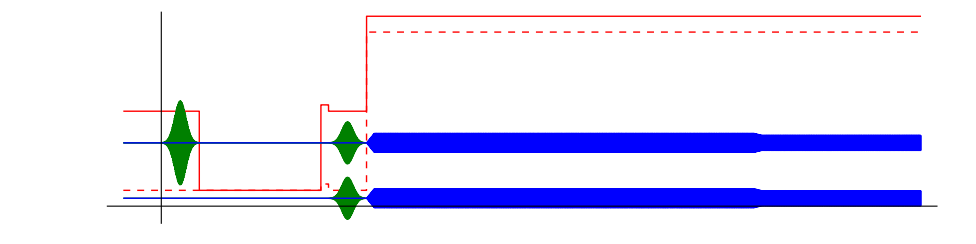

```mathematica
green1=RGBColor[0,0.5,0];
shift2=-0.175;shiftMW=5.4;
tMin=-10;tMax=200;
aPulseπ=0.5;dPulseMW=9;
dManip=dPulseMW+1;dCouple=32;dZ=2;dTomo=dPulseMW+1;dMeas=100;dRiseFall=0.01;
manipQB1=5.5;manipQB2=5.25;zPulse1=5.52;zPulse2=5.27;readoutQB1=5.8;readoutQB2=5.75;
aPulseπ=0.5;dPulseMW=10;tPulseMW1=0+dManip/2;tPulseTomo=dManip+dRiseFall+dCouple+dRiseFall+dZ+dRiseFall+dPulseMW/2;
tJBA=tPulseTomo-dPulseMW/2+dTomo+dRiseFall;

gr1=Plot[{frPulse[0,{{manipQB1,dManip},{manipQB2,dCouple},{zPulse1,dZ},{manipQB1,dTomo},{readoutQB1,dMeas}}][t],frPulse[0,{{manipQB2,dManip},{manipQB2,dCouple},{zPulse2,dZ},{manipQB2,dTomo},{readoutQB2,dMeas}}][t]},{t,tMin,tMax},PlotStyle->{Red,{Dashed,Red}},PlotRange->All,PlotPoints->500,AspectRatio->1/4,Axes->{True,False},AxesOrigin->{0,5.2},Ticks->{Table[{i,""},{i,0,600,100}],None}];
gr2=Plot[{pulseGauss[aPulseπ,tPulseMW1,1.5,manipQB1,0][t]+shiftMW,pulseGauss[aPulseπ/2,tPulseTomo,1.5,manipQB1,π/2][t]+shiftMW,jbaPulse[0.03,tJBA,2,100,200,0.8][t]+shiftMW,pulseGauss[aPulseπ/2,tPulseTomo,1.5,manipQB2,π/2][t]+shift2+shiftMW,jbaPulse[0.03,tJBA,2,100,200,0.8][t]+shift2+shiftMW},{t,tMin,tMax},PlotStyle->{green1,green1,Blue,green1,Blue},PlotRange->All,PlotPoints->500,AspectRatio->1/4,Axes->{True,False},AxesOrigin->{0,-0.3+shiftMW},Ticks->{Table[{i,""},{i,0,600,100}],None}];
Show[gr1,gr2]
```